## Rajz súlypontja

```mathematica
GetCenterOfGravity[points_]:=Module[{part,linesegments,totalweight},
part=Partition[points,2,1];
linesegments={{(#1⟦1⟧+#2⟦1⟧)/2,(#1⟦2⟧+#2⟦2⟧)/2},Norm[#1-#2]}&@@@part;
totalweight=Total[linesegments⟦All,2⟧];
Total[#⟦1⟧*#⟦2⟧&/@linesegments]/totalweight//N
]
GetCenterOfGravity[{{0,0},{1,0},{2,5},{3,3}}]
```

{1.6483,2.60247}

```mathematica
Manipulate[
Graphics[{Line[u],Red,Point[GetCenterOfGravity[u]]},PlotRange->2],{{u,{{0,0},{1,1}}},Locator,LocatorAutoCreate->True}]
```

## Rajz befoglaló görbéje

```mathematica
test={{0,0},{1,0},{6,0},{2,1.7},{3,3},{3,2}};
```

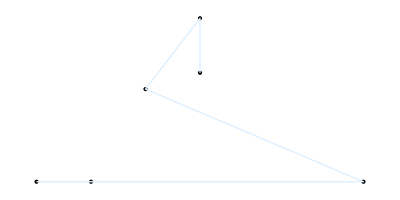

```mathematica
Graphics[{Point/@test,LightBlue,Line@test}]
```

```mathematica
isLeft[p0_,p1_,p2_]:=(p1⟦1⟧-p0⟦1⟧)(p2⟦2⟧-p0⟦2⟧)-(p2⟦1⟧-p0⟦1⟧)(p1⟦2⟧-p0⟦2⟧)
```

```mathematica
GetConvexHull[p_]:=Module[{temp,lowest,miny,P0,q,extq,i,Ω,pT1,pT2,safe,j},
(*Select the rightmost lowest point P0 in S*)
miny=Min[p⟦All,2⟧];
lowest=Select[p,#⟦2⟧==miny&];
P0=First@Sort[lowest,#1⟦1⟧>#2⟦1⟧&];
q=Select[p,#≠P0&];
extq=Table[{q[[j]],ArcTan[q⟦j⟧⟦1⟧-P0⟦1⟧,q⟦j⟧⟦2⟧-P0⟦2⟧]},{j,1,Length@q}];
q=Sort[extq,#1⟦2⟧<#2⟦2⟧&]//N;
q=q[[All,1]];
Ω={P0,q[[1]]};
i=2;
safe=100;
j=0;
While[
(i<=Length@q)&&(j<safe),
(*Print["Iter "<>ToString[j]];*)
j++;
(*Print[Ω];*)
pT1=Last@Ω;
If[pT1==Ω[[1]],AppendTo[Ω,pT1];i++(*Print["Init"];*)];
pT2=Ω⟦-2⟧;
If[isLeft[pT2,pT1,q⟦i⟧]>0,AppendTo[Ω,q⟦i⟧];i++;(*Print["Added"];*),
(*else*)Ω=Ω⟦;;-2⟧(*Print["Popped"];*)]
(*Print[Ω];*)
];
Ω
]
```

```mathematica
GetConvexHull[test]
```

{{6,0},{3.,3.},{0.,0.}}

Alt+Bal egér gomb

```mathematica
Manipulate[
Graphics[{Line[u],
Red,Point@GetCenterOfGravity[u],
Opacity[0.3],Blue,Polygon@GetConvexHull[u]},PlotRange->2],{{u,{{0,0},{1,1}}},Locator,LocatorAutoCreate->True}]
```